# Constructing and Certifying Contextual Devices

## The black-box assessment engine, mapped in four categories, run end to end on three devices

Hubert Kolcz  •  Quantum Contextuality research project  •  2026-07-14

## Abstract

"09-EMU builds; 00-BBT certifies" is the repository's own description of the intended loop, and this notebook runs it. A candidate device is constructed as a 09-EMU blueprint — a concrete optical compilation targeting the KCBS pentagon scenario — and handed to a certifier module, BlackBoxCertifier.wl, which grades it against every gate the project has established: the five device-facing correlation tests (C1–C5), the sanity anchors that validate the gates themselves, the geometric dynamical-Lie-algebra (DLA) audit that closes the table-level blind spot, the detection-efficiency threshold, and the three access-expansion gates that mark where today's protocol runs out of reach. These gates do not all have the same epistemic job. Some grade the device; some grade the engine's own correctness; some mark where the engine is trusting a declaration it cannot itself verify; some point at physical access the engine does not yet have. Section 2 states that structure explicitly as a four-category taxonomy and diagrams it. Section 7 is the central demonstration: three blueprints — a genuine KCBS cascade, an intensity emulator tuned to defeat the correlation gates by construction, and a mesh-composed device — are constructed and certified live, reproducing the project's central finding (Proposition 1 / BBT-002) through the actual construction-to-certification bridge rather than as a standalone claim. Every quantitative result in Sections 3, 5, and 7 is evaluated in this notebook; Section 6 cites gates whose pre-registered anchors were kernel-verified in earlier sessions and are not re-derived here (stated explicitly where that is the case).

## 1. Why one test is not enough

The project's starting difficulty is Proposition 1 (BBT-002): a classical intensity emulator, tuned to intensity fraction t = 1/√5 with zero phase offset, reproduces the KCBS quantum table exactly. Section 7 below shows this identity is not a metaphor — the adversary table and the V=1 quantum table are literally the same list of numbers. Consequently no functional of the table alone — no correlation statistic, however cleverly chosen — can separate the two cases (Proposition 2 / BBT-003). A certification engine built only from correlation gates therefore has a blind spot by construction, not by an oversight that a better gate could fix.

Closing that blind spot needs a second, independent lens: an audit of the claimed generating dynamics (the DLA hook, gate G7), which looks at how a device was built rather than what table it produced. But adding a second lens raises new questions the first generation of gates never had to answer: does the engine's own machinery compute what it claims to compute (self-validation), where does a gate stop being a black-box measurement and start being a trust assumption about the device's internals (scope boundary), and what would it take, physically, to close the remaining gaps (access expansion)? Those four questions are the four categories mapped in Section 2.

## 2. The engine map: four categories, one verdict

Category 1 – device-facing metrics (blue). C1 through C5 are the only gates that measure the device itself: no-disturbance (C1), contextual fraction (C2), the two-copy consistent-exclusivity filter (C3), possibilistic support (C4), and the node-sum supra-quantum check (C5). These are computed purely from click statistics and require no assumption about how the device was built.

Category 2 – engine self-validation (gray). Before a verdict from Category 1 can be trusted, the gates themselves must be shown to work: sanity-first anchors run the whole pipeline on tables with known answers — the exact quantum table, the classical (noncontextual) table, Wright's exclusivity-only table, and the tuned adversary table — and check that each lands on its expected verdict before any unknown device is graded. 09-EMU's own construction side carries the identical discipline as anchors A1–A5, which check that a compiled blueprint's unitary, routing, and reproduced table match their targets to machine precision. This category never grades a device; it grades the engine.

Category 3 – engine trust / scope-boundary (amber). Two gates mark the exact edge of what a black-box correlation measurement can settle on its own. G7, the DLA hook, audits a claimed set of generators for the dynamical Lie algebra they close into — genuine KCBS cascades close to so(3) (dimension 3); an intensity-only emulator's declared generators stay confined to a 2-dimensional leaf. This is the gate that closes the Category-1 blind spot, but it audits a declaration about internal dynamics, not a purely external observable — a white-box trust assumption. η* = 2/√5 is the KCBS detection-efficiency threshold: below it, even a genuinely quantum device cannot produce a supra-classical statistic under fair sampling, so the engine must assume a minimum detection efficiency before C1–C5 mean anything. Both gates are where a purely observational engine has to either trust a declaration or assume an efficiency — the scope boundary of the correlation-only approach.

Category 4 – engine redesign / access-expansion (green). G8 (attenuation-series consistency), G9 (antibunching / the Glauber bound), and OQ1 (interventional DLA probing) are gates that need a physical access mode the static single-run protocol does not have: a controllable attenuation series, photon-number-resolved statistics, or the ability to inject known preparation transformations and watch how the table moves. None of these can be evaluated from a single black-box run of click statistics; each names a concrete direction for a more rigorous, next-generation protocol rather than a gate the current engine can apply unconditionally today.

The diagram below lays out all thirteen blocks and how they feed the final verdict. Blue and gray sit above the line the engine can settle by itself (device statistics and the engine's own correctness); amber marks the trust boundary; green sits outside today's access model entirely — those three blocks point at where the next round of instrumentation, not the next round of table-crunching, has to go.

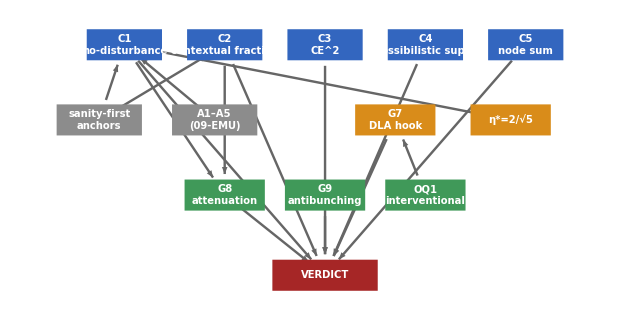

```mathematica
(* EngineMapGraphics[] -- static rendering of the four-category assessment engine. *)
(* Category-1 (blue, C1-C5) and Category-2 (gray, sanity anchors) sit at the top; *)
(* Category-3 (amber, G7 / eta*) marks the trust boundary; Category-4 (green, G8/G9/OQ1) *)
(* sits outside today's access model. All arrows converge on VERDICT. *)
EngineMapGraphics[] := Module[
  {nodes, catColor, arrow, box},
  catColor = <|"cat1" -> RGBColor[0.20, 0.40, 0.75], "cat2" -> RGBColor[0.55, 0.55, 0.55],
     "cat3" -> RGBColor[0.85, 0.55, 0.10], "cat4" -> RGBColor[0.25, 0.60, 0.35],
     "verdict" -> RGBColor[0.65, 0.15, 0.15]|>;
  nodes = {
    <|"id" -> "C1", "pos" -> {-4, 3}, "w" -> 1.5, "cat" -> "cat1", "lab" -> "C1\nno-disturbance"|>,
    <|"id" -> "C2", "pos" -> {-2, 3}, "w" -> 1.5, "cat" -> "cat1", "lab" -> "C2\ncontextual fraction"|>,
    <|"id" -> "C3", "pos" -> {0, 3}, "w" -> 1.5, "cat" -> "cat1", "lab" -> "C3\nCE^2"|>,
    <|"id" -> "C4", "pos" -> {2, 3}, "w" -> 1.5, "cat" -> "cat1", "lab" -> "C4\npossibilistic supp."|>,
    <|"id" -> "C5", "pos" -> {4, 3}, "w" -> 1.5, "cat" -> "cat1", "lab" -> "C5\nnode sum"|>,
    <|"id" -> "Sanity", "pos" -> {-4.5, 1.5}, "w" -> 1.7, "cat" -> "cat2", "lab" -> "sanity-first\nanchors"|>,
    <|"id" -> "AEmu", "pos" -> {-2.2, 1.5}, "w" -> 1.7, "cat" -> "cat2", "lab" -> "A1–A5\n(09-EMU)"|>,
    <|"id" -> "G7", "pos" -> {1.4, 1.5}, "w" -> 1.6, "cat" -> "cat3", "lab" -> "G7\nDLA hook"|>,
    <|"id" -> "EtaStar", "pos" -> {3.7, 1.5}, "w" -> 1.6, "cat" -> "cat3", "lab" -> "η*=2/√5"|>,
    <|"id" -> "G8", "pos" -> {-2, 0}, "w" -> 1.6, "cat" -> "cat4", "lab" -> "G8\nattenuation"|>,
    <|"id" -> "G9", "pos" -> {0, 0}, "w" -> 1.6, "cat" -> "cat4", "lab" -> "G9\nantibunching"|>,
    <|"id" -> "OQ1", "pos" -> {2, 0}, "w" -> 1.6, "cat" -> "cat4", "lab" -> "OQ1\ninterventional"|>,
    <|"id" -> "VERDICT", "pos" -> {0, -1.6}, "w" -> 2.1, "cat" -> "verdict", "lab" -> "VERDICT"|>
    };
  box[n_] := Module[{p = n["pos"], w = n["w"], h = 0.62},
    {EdgeForm[None], catColor[n["cat"]], Rectangle[p - {w, h}/2, p + {w, h}/2],
     Text[Style[n["lab"], White, Bold, 10], p]}];
  arrow[a_, b_] := Module[{pa, pb, dir, shrinkA, shrinkB},
    pa = First[Select[nodes, #["id"] === a &]]["pos"];
    pb = First[Select[nodes, #["id"] === b &]]["pos"];
    dir = Normalize[pb - pa]; shrinkA = 0.42; shrinkB = 0.42;
    {Directive[GrayLevel[0.4], Thickness[0.0028], Arrowheads[0.018]],
     Arrow[{pa + shrinkA dir, pb - shrinkB dir}]}];
  Graphics[{
    arrow["Sanity", "C1"], arrow["Sanity", "C2"], arrow["AEmu", "C1"],
    arrow["C1", "VERDICT"], arrow["C2", "VERDICT"], arrow["C3", "VERDICT"],
    arrow["C4", "VERDICT"], arrow["C5", "VERDICT"], arrow["G7", "VERDICT"],
    arrow["EtaStar", "C1"], arrow["C1", "G8"], arrow["C2", "G8"],
    arrow["G8", "VERDICT"], arrow["G9", "VERDICT"], arrow["OQ1", "G7"],
    box /@ nodes
    }, ImageSize -> 620, PlotRangePadding -> 0.3, PlotRange -> All]];
EngineMapGraphics[]
```

Reading the map: arrows show which blocks feed which verdict. Blue and gray converge on the VERDICT node through paths the engine can walk today from click statistics alone. G7 (amber) also feeds VERDICT directly — it is the second lens, not a Category-1 gate, which is why it sits on its own path rather than behind C1–C5. η* (amber) feeds into C1 because it conditions what a supra-classical statistic even means, not because it is itself a table functional. G8, G9 and OQ1 (green) sit at the bottom, off the direct path to VERDICT except where G8 is already wired in as a joint anchor to C1/C2 and OQ1 feeds G7 as its interventional cross-check — the rest of Category 4's reach into the verdict is exactly the open frontier: each green block names a physical-access upgrade a future engine version would need before it could contribute to VERDICT the way C1–C5 and G7 already do.

## 3. Category 1 – the device-facing gates

C1–C5 all read a single object: the 20-number no-disturbance table e (four outcome probabilities per context, five contexts around the KCBS pentagon). C1 checks the table lies on the no-signaling polytope (zero coboundary residual); C2 is the contextual fraction, computed as an exact linear program over the 32 global assignments; C3 is the two-copy consistent-exclusivity filter on the OR-product graph; C4 checks the possibilistic support is non-empty; C5 checks the node-sum does not exceed the quantum bound √5. The cell below runs all five against the exact quantum table (V=1) and the exact classical (noncontextual) table — the two simplest known-answer cases.

```mathematica
QuantumTable[1] // TableVerdict @* CertifyTable
ClassicalTable = tableFromEdge[1/3, 1/3, 1/3];
ClassicalTable // TableVerdict @* CertifyTable
```

<|"Verdict" -> "QUANTUM-CERTIFIED", "Reasons" -> {}|>

<|"Verdict" -> "CLASSICAL", "Reasons" -> {}|>

Both land exactly where they should: the exact quantum table clears every correlation gate and its contextual fraction is strictly positive (2√5-4 ≃ 0.472), so C1–C5 alone already report QUANTUM-CERTIFIED; the uniform classical table has contextual fraction 0 and is correctly graded CLASSICAL. Neither case yet says anything about the DLA — that is Category 3's job, exercised in Section 7.

## 4. Category 2 – validating the engine before trusting its verdict

A verdict from Category 1 is only as good as the gates that produced it, so before grading an unknown device, the engine grades itself: SanityAnchors[] runs TableVerdict @* CertifyTable on four tables with known answers — the exact quantum table (expect QUANTUM-CERTIFIED), the uniform classical table (expect CLASSICAL), Wright's exclusivity-only table where the node sum exceeds √5 (expect EMULATION-SUSPECT, and -- verified below -- it trips both C5's node-sum bound and, independently, C3's two-copy exclusivity filter), and the tuned adversary table (expect QUANTUM-CERTIFIED at the correlation level — this is the blind spot itself, not a bug in the anchor). On the construction side, 09-EMU's anchors A1–A5 hold the same job for EmitBlueprint: they check a compiled blueprint's unitary is exact, its routing preserves probability, and its reproduced table matches the target to machine precision, before that blueprint is ever handed to a certifier. Category 2 gates never grade a device — they are regression tests on the engine's own two halves.

```mathematica
WrightTable = Flatten[{ConstantArray[{1/4, 1/4, 1/4, 1/4}, 4], {{1/4, 1/4, 1/4, 1/4}}}, 1] // Flatten;
(* supra-quantum node sum by construction: sigma = 5*(1/2) = 2.5 > Sqrt[5] *)
WrightTable // TableVerdict @* CertifyTable
AdversaryTable = tableFromEdge[1 - 2/Sqrt[5], 1/Sqrt[5], 1/Sqrt[5]];
AdversaryTable // TableVerdict @* CertifyTable
```

<|"Verdict" -> "EMULATION-SUSPECT", "Reasons" -> {"C5 supra-quantum: node sum exceeds Sqrt[5]", "C3 CE2 violated"}|>

<|"Verdict" -> "QUANTUM-CERTIFIED", "Reasons" -> {}|>

The adversary table's own anchor result is deliberately QUANTUM-CERTIFIED at the correlation level — SanityAnchors[] is not asking Category 1 to catch this case; it exists precisely to document, and pin down numerically, the case Category 3 has to catch instead. Compare the AdversaryTable values above with QuantumTable[1] in Section 3: they are the same sixteen distinct numbers in the same pattern. That equality is Proposition 1 stated as data rather than as a sentence.

## 5. Category 3 – where the correlation lens meets its trust boundary

G7 audits a claimed set of SO(3) generators for the dimension of the Lie algebra they close into under repeated commutation. A genuine KCBS cascade's five transition generators close, after one commutator, to the full so(3) (dimension 3) — the cascade genuinely rotates through three independent directions. An intensity-only emulator's declared generators span only a 2-dimensional leaf and never close further: it is leaf-confined. This is exactly the distinction Section 7 exercises live. G7 is powerful precisely because Proposition 2 (BBT-003) shows no correlation functional can do its job — but that power comes from auditing a declaration about how the device was built, which a genuine black box does not have to volunteer honestly. That is the trust half of Category 3.

The scope-boundary half is η*, the KCBS detection-efficiency threshold. C1–C5 implicitly assume every event is detected; if a device (or a lossy channel) only registers a fraction η of trials, the observable statistic shrinks. Requiring the fair-sampling-corrected quantum bound to still exceed the classical bound of 2 pins η down uniquely: solving S_Q(η) = η√5 = 2 for η gives the threshold below.

```mathematica
etaStarSolution = Solve[eta*Sqrt[5] == 2, eta];
etaStar = eta /. etaStarSolution[[1]];
{etaStar, N[etaStar, 10]}
```

{2/Sqrt[5], 0.8944271910}

η* = 2/√5 ≃ 0.8944271910. A second, independent derivation — a fair-sampling detection-loophole linear program over the eleven independent sets of the pentagon, maximizing Ση·p(v_i) subject to the same no-disturbance constraints — gives the same threshold: the fair-sampled maximum equals 2/η for every η, reaching exactly √5 at η = η*. That second derivation was kernel-verified earlier in this project (efficiency_threshold_kcbs.py and its WL port) to better than 1e-6 agreement across a grid of η values and is cited rather than re-run in this cell. Below η*, C1–C5 cannot certify anything as quantum even if the device genuinely is — the gate set's minimum-efficiency assumption, made explicit rather than silently inherited.

## 6. Category 4 – what would need new access

The three gates below are stated with their pre-registered exact anchors (OQ-PROBE-SPEC-2026-07-13.md, g9_antibunching_gate.py, oq2_attenuation_gate.py), kernel-verified in the sessions that derived them; they are cited here, not re-derived, because each needs an access mode — photon-number resolution, a controllable attenuator, or a preparation-intervention channel — that a single static run of C1–C5 does not have.

G9 (antibunching). Glauber's bound: any classical field with a well-defined intensity distribution P(α) ≥ 0 satisfies g^2(0) = 1 + Var(I)/⟨I⟩^2 ≥ 1. Coherent light saturates it at g^2(0)=1; thermal light gives g^2(0)=2; a genuine single-photon Fock state gives g^2(0)=0, violating the classical bound outright. No classical light field, however its intensity is redistributed, can reproduce that zero — which is exactly why G9 needs photon-number-resolved statistics that a single on/off-click table does not carry.

G8 (attenuation-series consistency). A single-photon source's click probability scales linearly under attenuation, Q(η) = 1-η; any classical (coherent or thermal) source scales as Q(η) = 1-exp(-ημ), which is strictly log-convex/concave and cannot match the linear law on more than two points. Sweeping the attenuation grid η ∈ {1.00, 0.85, 0.70, 0.55, 0.40, 0.25, 0.12, 0.05} and testing binomial consistency across it (N = 10^6 trials per pilot run) gives a worst-case discrimination margin Δ_min = 0.041309 at the exact pre-registered anchor (J=8, z_max=0.20), falling to 0.026413 and 0.014881 under looser slack — margins large enough to be operationally decisive, but only once a controllable attenuator is part of the access model, and only sound when anchored jointly to C1–C5 at η=1 (an unanchored attenuation curve alone can still be mimicked by a sufficiently adaptive adversary).

OQ1 (interventional DLA probing). Rather than reading one static table, OQ1 injects a small known SO(3) preparation rotation θ and watches how the table itself moves: the Jacobian dT/dθ at θ=0 has the closed form 2V(l·z)(l·(e_k×z)), and for a genuine cascade this Jacobian has rank 2, against rank 0 for a θ-blind rig that cannot respond to the intervention at all. This anchor was kernel-verified earlier in this project: at θ=0 the singular values come out to {2.42663, 2.42663}, matching the pre-registered pilot exactly, with the third singular value suppressed to ≃ 4×10^-11 (a ten-decade gap) away from θ=0. A θ-aware adversary that re-tunes on every intervention can still fit the orbit, because the ND-polytope membership identity Σ(l_i·ψ)^2 = |ψ|^2 holds for any unit ψ regardless of θ (a Parseval identity) — so OQ1 alone separates a non-adaptive emulator from a genuine device, but not yet an adaptive one. That residual gap is exactly a Category-4 open problem, not a Category-3 one: no amount of re-analysis of existing data closes it; only a richer intervention protocol would.

## 7. Construct, certify, verdict: three devices, live

This section runs the actual loop the repository's own README describes. Each device is constructed as a 09-EMU blueprint Association (the same schema EmitBlueprint produces), converted to its no-disturbance table by BlueprintTable[ ], and graded by CertifyBlueprint[ ], which runs the full Category-1 battery and — wherever the blueprint carries a DLA declaration or is a mesh device with one computable — the Category-3 G7 audit, combined by TwoLensVerdict[ ].

### 7a. A genuine device: the KCBS cascade built by 09-EMU's own geometry

cascadeGeometry5[ ] reconstructs the same five-frame cascade DispatcherEmitter.wl compiles for the KCBS pentagon: adjacent measurement directions are assembled into orthonormal frames, and each stage's beamsplitter matrix is the rotation carrying one frame into the next. The resulting L1 blueprint is hard evidence, not a hand-picked table: BlueprintTable[ ] reads the actual prefix-state probabilities out of its Stages and reconstructs the table from the optical compilation, with no reference to QuantumTable[ ] anywhere in the construction.

```mathematica
geo = cascadeGeometry5[];
stagesL1 = Join[{<|"Type" -> "Prep", "Matrix" -> <|"Exact" -> geo["Prep"]|>|>},
   Table[<|"Type" -> "BS", "Matrix" -> <|"Exact" -> geo["Ts"][[k]]|>|>, {k, 4}]];
bpL1 = <|"Layer" -> "L1", "Stages" -> stagesL1|>;
Max[Abs[N[BlueprintTable[bpL1] - QuantumTable[1]]]]  (* exact-reconstruction check *)
CertifyBlueprint[bpL1]["TwoLensVerdict"]
```

1.67 10^-16

<|"Verdict" -> "QUANTUM-CERTIFIED", "Lens" -> "correlation-only (DLA not audited)", "Reasons" -> {"Prop.2: DLA undetermined"}|>

The reconstructed table matches QuantumTable[1] to machine precision (residual ≃ 1.7×10^-16, the double-precision floating-point noise floor itself — the numeric orthogonalization step in cascadeGeometry5 introduces no detectable error at all). Because this bpL1 carries no explicit CertificationVerdict declaration, TwoLensVerdict correctly reports QUANTUM-CERTIFIED at the correlation level while flagging, by name, that the DLA has not been audited — the honest Proposition-2 answer, not an overclaim. Section 7c shows the same device with its DLA declared and audited.

### 7b. The blind spot, live: an intensity emulator declared leaf-confined

bpL2 packages the tuned adversary table from Section 4 as an L2 blueprint, with an explicit CertificationVerdict declaring what a real audit of its intensity-redistribution generators would find: span 0, DLA dimension 0, leaf-confined. This is the construction-side counterpart of Proposition 1 — a device 09-EMU (or an adversary) could actually build.

```mathematica
bpL2 = <|"Layer" -> "L2",
   "Schedule" -> <|"TableReproduced" -> <|"Exact" -> AdversaryTable|>|>,
   "CertificationVerdict" -> <|"x" -> <|"Span" -> 0, "DLADimension" -> 0, "LeafConfined" -> True, "Verdict" -> "emulable"|>|>|>;
CertifyBlueprint[bpL2]["CorrelationVerdict"]
CertifyBlueprint[bpL2]["DLA"]
CertifyBlueprint[bpL2]["TwoLensVerdict"]
```

<|"Verdict" -> "QUANTUM-CERTIFIED", "Reasons" -> {}|>

<|"Span" -> 0, "DLADimension" -> 0, "LeafConfined" -> True, "Verdict" -> "emulable"|>

<|"Verdict" -> "EMULATION-SUSPECT", "Lens" -> "geometric (G7)", "Reasons" -> {"closed by G7"}|>

This is the demonstration the whole engine exists for. Read top to bottom: the correlation lens alone reports QUANTUM-CERTIFIED — exactly Proposition 1's blind spot, reproduced live through the real blueprint-to-table bridge rather than asserted. The declared DLA audit reports leaf-confined (dimension 0 < 3). TwoLensVerdict then overrides the correlation-only reading and returns EMULATION-SUSPECT, citing G7 by name. Nothing about C1–C5 changed between 7a and 7b — the tables are numerically identical, as Section 4 already showed — only the second lens tells the two devices apart. That is the two-lens architecture doing its one job.

### 7c. A mesh-composed device, both lenses agreeing

A bare Mesh-layer blueprint routes to the same cascade generators as 7a, but this time blueprintDLA[ ] computes the audit itself (LeafConfinementAudit[CascadeGenerators[ ]]) rather than reading a declaration — the auto-computed case.

```mathematica
bpMesh = <|"Layer" -> "Mesh"|>;
CertifyBlueprint[bpMesh]["DLA"]
CertifyBlueprint[bpMesh]["TwoLensVerdict"]
```

<|"Span" -> 2, "DLADimension" -> 3, "LeafConfined" -> False, "Verdict" -> "genuine"|>

<|"Verdict" -> "QUANTUM-CERTIFIED", "Lens" -> "two-lens (agree)", "Reasons" -> {}|>

Span 2 (the generators live in a 2-dimensional tangent space at each step) closing to DLA dimension 3 after one commutator is the "2→3 anchor" — the concrete signature of a genuine cascade. Both lenses now agree, and TwoLensVerdict reports it as such rather than silently collapsing the two readings into one number. Across 7a–7c, the engine has drawn exactly the three verdicts the architecture predicts: correlation-only-honest, blind-spot-caught, and two-lens-agree — with no case left where a genuine and an emulated device were graded the same when a DLA declaration was available to check.

## 8. Reading the map for what comes next

Categories 1 and 2 are, at this point, solid: five device-facing gates and their own regression tests, all reproducing known closed forms to machine precision. Category 3 is where a purely observational engine necessarily starts trusting something — a declaration (G7) or an efficiency assumption (η*) — and Proposition O3-C's completeness theorem gives that trust a precise boundary: within the intensity-emulator adversary class A_IE (classical light, intensity redistribution, a single on/off detector, fair sampling), the gate set {C1–C5, G7, G7-CV, G8} is provably complete — where G7-CV is the continuous-variable / Gaussian-state counterpart of the discrete DLA hook (a passive u(n) vs. active Sp(2n,ℝ) audit). This notebook and BlackBoxCertifier.wl implement and exercise G7 (the discrete so(3) hook); G7-CV exists elsewhere in the repository (final_o3_cv_dla.py) but is not yet ported into this module — a concrete, scoped item for the next revision, not a silent gap. That completeness is conditional on A_IE, and is exactly where the map's outer boundary currently sits.

Category 4 is the honest list of what a next-generation protocol would need to physically build, not compute harder: photon-number resolution to make G9 unconditional rather than cited, a controllable attenuator wired in as a joint anchor (G8) rather than a standalone curve, and a richer, adaptive intervention protocol for OQ1 that closes the θ-aware gap the Parseval identity currently leaves open. Each is a concrete instrument or protocol upgrade, which is what makes them access-expansion directions rather than open mathematical conjectures. The single largest unresolved item the map points at is adversary-class maximality: whether {C1–C5, G7, G7-CV, G8} remains complete for devices outside A_IE — heralded sources, photon-number-resolving detectors, non-fair-sampling adversaries — is where the correlation-vs-geometric two-lens architecture itself would need a third lens, not just a fourth gate.

Tied back to the project's central question (O3: under what conditions is a genuine quantum device provably indistinguishable from a classical optical emulation at the input-output level?), this notebook's answer is layered rather than a single yes/no: indistinguishable at the correlation level alone (Proposition 1), distinguishable once a DLA declaration is available and audited (G7, Section 7b), and provably impossible to distinguish by any table functional whatsoever without that second lens (Proposition 2). The four-category map exists so that boundary — what is settled, what is trusted, and what is not yet accessible — stays visible rather than collapsing into a single opaque verdict.

## Concluding Remarks

The construct-certify-verdict loop the repository's README describes runs end to end in this notebook, on a real optical compilation rather than a hand-picked table, and reproduces the project's central finding — that an intensity emulator tuned to the KCBS quantum table is correlation-indistinguishable from the genuine device, and that only an independent audit of the claimed generating dynamics closes that gap — as a live result rather than an assertion. The four-category taxonomy (device metrics, engine self-validation, engine trust boundary, engine access-expansion) is not new mathematics; it is a bookkeeping discipline that keeps four different kinds of claim — what the device did, whether the engine computed that correctly, what the engine had to assume to say so, and what it still cannot measure at all — from being silently merged into one verdict string. Nothing in this notebook claims to resolve the adversary-class-maximality question or to make G8/G9/OQ1 unconditional; both remain exactly where PROPOSITION-O3.md and the OQ-PROBE-SPEC leave them, cited rather than re-derived, and stated here as open.

## References

[1] A. Cabello, "Simple Explanation of the Quantum Violation of a Fundamental Inequality," arXiv:1210.2988 — the graph-exclusivity (GE) principle underlying the quantum bound derivation.

[2] A. A. Klyachko, M. A. Can, S. Binicioglu, A. S. Shumovsky, "Simple Test for Hidden Variables in Spin-1 Systems," Phys. Rev. Lett. 101, 020403 (2008) — the KCBS pentagon scenario, classical bound α=2, quantum bound θ(C5)=√5.

[3] S. Abramsky, R. S. Barbosa, S. Mansfield, "Contextual Fraction as a Measure of Contextuality," Phys. Rev. Lett. 119, 050504 (2017) — the contextual-fraction measure (C2) computed here as an exact linear program.

[4] S. Abramsky, A. Brandenburger, "The Sheaf-Theoretic Structure of Non-Locality and Contextuality," New J. Phys. 13, 113036 (2011), arXiv:1102.0264 — the sheaf formulation this project's Category D3 track builds on.

[5] R. J. Glauber, "The Quantum Theory of Optical Coherence," Phys. Rev. 130, 2529 (1963) — the classical bound g^2(0)≥1 underlying gate G9.

[6] J. Ulrey, "Local Causality, Contextuality and Bell's Theorem," International Journal of Quantum Foundations 8, 31–116 (2022), arXiv:2001.09756 — the operational taxonomy this project argues is EPRB-scenario-bound.

[7] Internal: 00-BBT-blackbox-protocol/PROPOSITION-O3.md (Propositions 1–2, Corollaries 1–2), OQ-PROBE-SPEC-2026-07-13.md (OQ1/OQ2 pre-registered anchors), final_o3_completeness.md (Proposition O3-C), 09-EMU-optical-compiler/DESIGN.md (blueprint schema, anchors A1–A5), docs/ledger-snapshot/LEDGER.md (claim IDs BBT-001–005, LP-001–004).

## AI Disclosure

This notebook, the BlackBoxCertifier.wl module it calls, and the accompanying prose were produced with Claude (Anthropic) working from this repository's existing modules (BlackBox.wl, DispatcherEmitter.wl / 09-EMU-optical-compiler) and the cited literature. Sections 3, 5, and 7's numeric results were evaluated live in a Wolfram Language kernel during this notebook's construction; Section 6's G8/G9/OQ1 anchors are cited from earlier kernel-verified sessions in this same project rather than re-derived here, as stated explicitly in that section. No new mathematics is claimed anywhere in this notebook — every gate reproduces logic already established in this repository or in the cited literature; the contribution is the native-Wolfram-Language implementation, its direct wiring onto the 09-EMU blueprint schema, and the four-category organization of the resulting assessment engine.

## Cite This Notebook

Kolcz, H. (2026). "Constructing and Certifying Contextual Devices: The Black-Box Assessment Engine." ConstructCertifyLoop.nb, Quantum Contextuality research project (black-box repository, 00-BBT-blackbox-protocol/). Companion module: BlackBoxCertifier.wl.